```mathematica
Quit[]
```

#### Kernels Control

```mathematica
LaunchKernels[8]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local]}

```mathematica
CloseKernels[Kernels[]]
```

```mathematica
Kernels[]
```

### Main

#### Declaration

```mathematica
ParallelEvaluate[Off[General::stop,NIntegrate::slwcon]];
```

```mathematica
ParallelEvaluate[On[General::stop]];
```

```mathematica
If[$OperatingSystem=="Windows",{dir="D:/Documents/2-d-data";},{dir="~/Documents/2-d-data";}];
```

```mathematica
SetOptions[NIntegrate,MaxRecursion->50];
```

The amplitude

```mathematica
(*If targeting the position, then use [ω1,ω2]*)
```

```mathematica
𝒞[expr_[ω__][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],{ω1->ω2/(1+ω2-ω1),ω2->ω1/(1+ω2-ω1),ϕ1->ϕ3,ϕ3->ϕ1,ϕ2->ϕ4,ϕ4->ϕ2,M1->M3,M3->M1,M2->M4,M4->M2}]
𝒫[expr_[ω__][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],{ω1->(1+ω2-ω1)/ω2,ω2->1/ω2,ϕ1->ϕ2,ϕ2->ϕ1,ϕ3->ϕ4,ϕ4->ϕ3,M1->M2,M2->M1,M3->M4,M4->M3}]
ℛ[expr_[ω__][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],{ω1->ω1/ω2,ω2->1/ω2,ϕ3->ϕ4,ϕ4->ϕ3,M3->M4,M4->M3}]
𝒮[expr_[ω__][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],{ω1->1/ω1,ω2->(1+ω2-ω1)/ω1,ϕ1->ϕ4,ϕ4->ϕ1,ϕ2->ϕ3,ϕ3->ϕ2,M1->M4,M4->M1,M2->M3,M3->M2}]
```

```mathematica
EXPR[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]:=If[ω1>1,ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,Mb,Ma,Mc,Md]+ℳ0[1/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb]+ℐ1[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ2[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb],ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℐ2[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]]+If[ω2>ω1,ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md],ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,Mb,Ma,Md,Mc]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]+ℐ1[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma]+ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]]+Which[0<ω1<1&&ω2≥ω1,ℐ3[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ3[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma],ω2≥ω1&&ω1≥1,ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℐ3[(1+1/ω2-ω1/ω2) ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,Mb,Ma,Mc,Md],0<ω1<1&&ω1>ω2,ℐ3[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,Mb,Ma,Md,Mc],ω1≥1&&ω1>ω2,ℐ3[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb]+ℐ3[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]];
```

```mathematica
ℳ0[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]:=4 g^2 ω1 NIntegrate[1/(y ω1-ω2-x)^2 ϕ1[(ω2-ω1+x)/(ω2-ω1+1)]ϕ2[y]ϕ3[x]ϕ4[(y ω1)/ω2],{x,0,1},{y,0,1}]
```

```mathematica
(*𝒞[f_Symbol[arg__]]:=f[#2/(1+#2-#1),#1/(1+#2-#1)]&[arg]
𝒫[f_Symbol[arg__]]:=f[(1+#2-#1)/#2,1/#2]&[arg]*)
```

```mathematica
(*ℳ1[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]=((#+𝒮[#])&[(*If[1>ω1,-4 g^2 NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,1}],0]*)
ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]])+((#+𝒞[#])&[(*If[ω2>ω1,-4 g^2 NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,1}],0]*)
ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]])+((#+𝒮[#]+𝒫[#]+𝒞[#])&[ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]]);*)
ℐ1[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]:=-4 g^2(NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,If[#>0,#,0]&[(-ω1+λ ω1+ω2)/ω2 ],If[#<1,#,1]&[(-λ ω1+ω2)/ω2 ]},{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,If[#>0,#,0]&[(-ω1+λ ω1+ω2)/ω2 ],If[#<1,#,1]&[(-λ ω1+ω2)/ω2 ]},{y,(ω1-ω2+x ω2)/ω1+λ,1}]-2/λ NIntegrate[ω2/ω1 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,If[#>0,#,0]&[(-ω1+λ ω1+ω2)/ω2 ],If[#<1,#,1]&[(-λ ω1+ω2)/ω2 ]}]+If[(-ω1+λ ω1+ω2)/ω2>0,NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,(-ω1+λ ω1+ω2)/ω2},{y,0,1}],0]+If[(-λ ω1+ω2)/ω2<1,NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,(-λ ω1+ω2)/ω2,1},{y,0,1}],0]);
ℐ2[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]:=-4 g^2(NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,If[#>0,#,0]&[ω1 λ],If[#<1,#,1]&[ω1 (1-λ)]},{y,0,x/ω1-λ}]+NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,If[#>0,#,0]&[ω1 λ],If[#<1,#,1]&[ω1 (1-λ)]},{y,x/ω1+λ,1}]-2/λ NIntegrate[1/ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[((x/ω1-1) ω1+ω2)/ω2],{x,If[#>0,#,0]&[ω1 λ],If[#<1,#,1]&[ω1 (1-λ)]}]+If[ω1 λ>0,NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,ω1 λ},{y,0,1}],0]+If[ω1 (1-λ)<1,NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,ω1 (1-λ),1},{y,0,1}],0]);
ℐ3[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]:=-(4 π)/Nc NIntegrate[(Mc^2+Md^2/ω2+(m^2-β^2)/(x-ω1)+(m^2-β^2)/(x-1)-(m^2-β^2)/(x-ω1+ω2)-(m^2-β^2)/x)ϕ1[(x-ω1+ω2)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[(x-ω1+ω2)/ω2],{x,0,1}];
```

```mathematica
EXPR1[ω1_,ω2_][m_,Ma_,Mb_,Mc_,Md_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]=EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md];
```

```mathematica
ℳone[ω1_,ω2_][m_,Ma_,Mb_,Mc_,Md_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=EXPR1[ω1,ω2][m,Ma,Mb,Mc,Md][ϕ1,ϕ2,ϕ3,ϕ4]
```

Solve ‘t Hooft equation

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
```

```mathematica
g=1;Nc=(β^2 π)/g^2;ℂ=0;(*ℂ denotes the interchange of final states.*)λ=10^-6;
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
Determineϕx[m1_,m2_,β_,Nx_]:=
Module[{HMatx,VMatx,vals,vecs,g,ϕx,ϕ},
SetSharedVariable[vecs,m1,m2,β,g];
SetSharedFunction[g];
HMatx=ParallelTable[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
VMatx=ParallelTable[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
Do[g[j]=Dot[ParallelTable[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}];
ϕx=ParallelTable[Quiet[g[Nx-n]/√NIntegrate[g[Nx-n]^2,{x,0,1}]],{n,0,20}];
Clear[g];
{√Reverse[vals] β,ϕx}
]
```

```mathematica
accDetermineϕ[m1_,m2_,β_,Nb_]:=
Module[{psi,ϵ=10^-6,Kernel1,Kernel2,hMT,sMT,sMatrix,hMTUp,hMT1,hMatrix,eg,vals,vecs,func,μ,nfunc},
Kernel1[n_][x_?NumberQ]:=NIntegrate[psi[n,y]/(x-y)^2,{y,0,x-ϵ}];
Kernel2[n_][x_?NumberQ]:=NIntegrate[psi[n,y]/(x-y)^2,{y,x+ϵ,1}];
psi[n_,x_]:=psi[n,x]=Which[n==0,x^(2-β)*(1-x)^β,n==1,(1-x)^(2-β)*x^β,n≥2,Sin[(n-1)*π*x]];
hMT[m_,n_]:=hMT[m,n]=NIntegrate[psi[m,x]((m1^2-1)/(x*(1-x))*psi[n,x]-Kernel1[n][x]-Kernel2[n][x]+(2psi[n,x])/ϵ),{x,ϵ,1-ϵ},WorkingPrecision->20];
sMT[m_,n_]:=sMT[m,n]=NIntegrate[psi[m,x]psi[n,x],{x,0,1}];
sMatrix=ParallelTable[Quiet[sMT[m,n]],{m,0,Nb},{n,0,Nb}]//Chop;hMTUp=PadLeft[#,Nb+1]&/@ParallelTable[Quiet[hMT[m,n]],{m,0,Nb},{n,m,Nb}];
(*Print[hMTUp];*)
hMatrix=Transpose[hMTUp]+hMTUp-DiagonalMatrix[Diagonal[hMTUp]];
(*Print[MatrixForm[hMatrix]];*)
eg[μ_]:=Det[hMatrix-μ^2*sMatrix];
μ=Sort@DeleteDuplicatesBy[Table[μ/.FindRoot[eg[μ]==0,{μ,a,a+0.2}],{a,0,Nb^2,0.2}],SetPrecision[#,2]&];
Print[μ];
vecs=(Flatten@NullSpace[hMatrix-#^2 sMatrix,Tolerance->0.001])&/@μ;
Print[vecs];Print[Dimensions@vecs];
func=ParallelTable[Table[psi[i,x],{i,0,Nb}].vecs[[j]],{j,1,Length[vecs]}];
nfunc=ParallelTable[Quiet[func[[n]]/√NIntegrate[func[[n]]^2,{x,0,1}]],{n,1,20}];
Clear[func,vecs];
{μ,nfunc}
]
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

Used z=(r_(2-))/(r_(1-)+r_(2-)), ω=(r_(4-))/(r_(1-)+r_(2-)), ω_1=(r_(2-))/(r_(3-)), ω_2=(r_(4-))/(r_(3-)) here.

```mathematica
ω2p[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2 ω1-M2^2))(-√((M1^2 (-ω1)+M2^2 ω1-M2^2-M3^2 ω1^2+M3^2 ω1+M4^2 ω1)^2-4 (M4^2 ω1-M4^2 ω1^2) (M3^2 ω1-M2^2))+M1^2 ω1-M2^2 ω1+M2^2+M3^2 ω1^2-M3^2 ω1-M4^2 ω1)(*transform ω1 to ω2, your definition, solution 1*)
```

```mathematica
Sω1[ω1_][M1_,M2_,M3_,M4_]:=(M1^2/(1-ω1+ω2p[ω1][M1,M2,M3,M4])+M2^2/ω1)(1+ω2p[ω1][M1,M2,M3,M4]);
```

```mathematica
ω1S[s_][M1_,M2_,M3_,M4_]:=(-M1^2+M2^2+s-√s √((M1^4+(M2^2-s)^2-2 M1^2 (M2^2+s))/s))/(M3^2-M4^2+s+√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s));
ω2S[s_][M1_,M2_,M3_,M4_]:=(-M3^2+M4^2+s-√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s))/(M3^2-M4^2+s+√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s));
```

```mathematica
Msum[mQ_][n1_?IntegerQ,n2_?IntegerQ,n3_?IntegerQ,n4_?IntegerQ]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2,M4,ϕ4,ω1,ω2,Sen,filenameacc,Determine,Mseq},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mQ;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
filenameacc=If[m1==m2,"/acceigenstate_m-"<>ToString[m1],"/acceigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filenameacc,dir,Infinity]=={},If[ChoiceDialog["Choose to use BSW method or to use the original solution suggested by 't Hooft, ",{"BSW method"->True,"Brute force integration"->False}],Determine=Determineϕx,filename=filenameacc;Determine=accDetermineϕ]];
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determine[m1,m2,β,Nx];
Set@@{ΦB[x_],Boole[0≤x≤1]ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],Boole[0≤x≤1]ϕxB};
}
];
(*Set@@{ΦB[x_],If[0≤x≤1,ΦB[x],0]};*)
Print["Wavefunction build complete."];
(*Print[ϕn[#][ΦB][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[n1];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[n2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[n3];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[n4];
Mseq=Sequence[M1,M2,M3,M4];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
{{M1,M2,M3,M4},ParallelTable[Sen=Ssqur^2;ω1=ω1S[Sen][M1,M2,M3,M4];ω2=ω2S[Sen][M1,M2,M3,M4];
{Ssqur,EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][mQ,M1,M2,M3,M4]},{Ssqur,M1+M2,M1+M2+5,0.01}]}
]
```

#### Calc

```mathematica
Clear["Global`g$*"]
```

```mathematica
Information["Global`g$*"]
```

```mathematica
Clear[ϕx,m2,ϕ,vals,M1,M2,M3,ϕ1,ϕ2,ϕ3];
```

#### 2→2

The total amplitude (and the square):

Function structure is Msum[<one flavour quark mass>][(excited state)<1>,<2>,<3>,<4>]

```mathematica
Msumdat=Msum[60][0,0,0,0]
```

```mathematica
ListPlot[{Select[Abs@Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],Last[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,242},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]]]
```

```mathematica
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(Last[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,242},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]]]
```

### Debug

```mathematica
λ=10^-5;
```

```mathematica
Clear[ValsB,ϕxB,ΦB,ΦBi];
Block[{mQ=100},m1=mQ;m2=mQ;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
filenameacc=If[m1==m2,"/acceigenstate_m-"<>ToString[m1],"/acceigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filenameacc,dir,Infinity]=={},If[ChoiceDialog["Choose to use BSW method or not"],Determine=Determineϕx,filename=filenameacc;Determine=accDetermineϕ]];
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determine[m1,m2,β,Nx];
Set@@{ΦB[x_],Boole[0≤x≤1]ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],Boole[0≤x≤1]ϕxB};
}
];
(*Set@@{ΦB[x_?NumberQ],If[0<=x<=1,ΦBi[x],Table[0,{n,Length@ϕxB}]]};*)
Print["Wavefunction build complete."];
(*Print[ϕn[#][ΦB][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[1];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[1];]
```

Wavefunction build complete.

```mathematica
ϕxB
```

{1.12866 (-0.324733 √(1-(-1+2 x)^2)-6.63765×10^-13 Sin[2 ArcCos[-1+2 x]]+0.321146 Sin[3 ArcCos[-1+2 x]]+8.6458×10^-13 Sin[4 ArcCos[-1+2 x]]-0.31435 Sin[5 ArcCos[-1+2 x]]-6.96867×10^-13 Sin[6 ArcCos[-1+2 x]]+0.304814 Sin[7 ArcCos[-1+2 x]]+702+1.32283×10^-12 Sin[492 ArcCos[-1+2 x]]-1.79189×10^-11 Sin[493 ArcCos[-1+2 x]]-1.15371×10^-12 Sin[494 ArcCos[-1+2 x]]+3.25076×10^-11 Sin[495 ArcCos[-1+2 x]]+4.12621×10^-13 Sin[496 ArcCos[-1+2 x]]-5.57951×10^-11 Sin[497 ArcCos[-1+2 x]]+1.1366×10^-13 Sin[498 ArcCos[-1+2 x]]+1.01813×10^-10 Sin[499 ArcCos[-1+2 x]]-1.12606×10^-13 Sin[500 ArcCos[-1+2 x]]),1.12902 (748+1),17,1.13184 (1),1.13196 (0.0878889 √(1-(-1+2 x)^2)+748)}
 |  |  |  |

```mathematica
(#;ParallelEvaluate@#)&@SetOptions[NIntegrate,MaxRecursion->100,AccuracyGoal->12,WorkingPrecision->20];
```

```mathematica
(#;ParallelEvaluate@#)&@SetOptions[NIntegrate,MaxRecursion->100,AccuracyGoal->12,WorkingPrecision->MachinePrecision];
```

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M3+M4+1)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]]//AbsoluteTiming
```

0.84671

0.868354

NIntegrate::inumr: The integrand (1.62377 Boole[0≤x≤1] Boole[0≤0.84671 (0.181042+x)≤1] Boole[0≤0.849957 y≤1] Boole[0≤y≤1] (-0.324733 √(1-Power[«2»])-6.63765×10^-13 Sin[2 ArcCos[Plus[«2»]]]+«73»+«450»)^2 (-2.3831×10^-12 √(1-Power[«2»])-0.0351956 Sin[2 ArcCos[Plus[«2»]]]+2.325×10^-12 Sin[3 ArcCos[Plus[«2»]]]+«71»+«450»)^2)/(-1.20661-x+1.02556 y)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

NIntegrate::inumr: The integrand (1.62377 Boole[0≤x≤1] Boole[0≤0.849957 (0.17653+x)≤1] Boole[0≤0.84671 y≤1] Boole[0≤y≤1] (-0.324733 √(1-Power[«2»])-6.63765×10^-13 Sin[2 ArcCos[Plus[«2»]]]+«73»+«450»)^2 (-2.3831×10^-12 √(1-Power[«2»])-0.0351956 Sin[2 ArcCos[Plus[«2»]]]+2.325×10^-12 Sin[3 ArcCos[Plus[«2»]]]+«71»+«450»)^2)/(-1.1516-x+0.975074 y)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{28.5529,-4 NIntegrate[(200.287^2+200.287^2/1.20661+(100^2-β^2)/(x-1.02556)+(100^2-β^2)/(x-1)-(100^2-β^2)/(x-1.02556+1.20661)-(100^2-β^2)/x) ϕn[1][ΦB][(x-1.02556+1.20661)/(1+1.20661-1.02556)] ϕn[1][ΦB][x/1.02556] ϕn[0][ΦB][x] ϕn[0][ΦB][(x-1.02556+1.20661)/1.20661],{x,0,1}]-4 NIntegrate[(200.287^2+200.287^2/1.20661+(100^2-β^2)/(x-1.18104)+(100^2-β^2)/(x-1)-(100^2-β^2)/(x-1.18104+1.20661)-(100^2-β^2)/x) ϕn[1][ΦB][(x-1.18104+1.20661)/(1+1.20661-1.18104)] ϕn[1][ΦB][x/1.18104] ϕn[0][ΦB][x] ϕn[0][ΦB][(x-1.18104+1.20661)/1.20661],{x,0,1}]+4.10225 NIntegrate[(ϕn[1][ΦB][(1.20661-1.02556+x)/(1.20661-1.02556+1)] ϕn[1][ΦB][y] ϕn[0][ΦB][x] ϕn[0][ΦB][(y 1.02556)/1.20661])/(y 1.02556-1.20661-x)^2,{x,0,1},{y,0,1}]+4.72417 NIntegrate[(ϕn[1][ΦB][(1.20661-1.18104+x)/(1.20661-1.18104+1)] ϕn[1][ΦB][y] ϕn[0][ΦB][x] ϕn[0][ΦB][(y 1.18104)/1.20661])/(y 1.18104-1.20661-x)^2,{x,0,1},{y,0,1}]+3.38684 NIntegrate[(ϕn[0][ΦB][(0.868354-0.84671+x)/(0.868354-0.84671+1)] ϕn[0][ΦB][y] ϕn[1][ΦB][x] ϕn[1][ΦB][(y 0.84671)/0.868354])/(y 0.84671-0.868354-x)^2,{x,0,1},{y,0,1}]-4 (-200000 NIntegrate[(ϕn[0][ΦB][(x+0.868354-0.84671)/(1+0.868354-0.84671)] ϕn[0][ΦB][x/0.84671] ϕn[1][ΦB][x] ϕn[1][ΦB][((x/0.84671-1) 0.84671+0.868354)/0.868354])/0.84671,{x,(If[#1>0,#1,0]&)[0.84671 λ],(If[#1<1,#1,1]&)[0.84671 (1-λ)]}]+NIntegrate[(0.84671 ϕn[0][ΦB][(x+0.868354-0.84671)/(1+0.868354-0.84671)] ϕn[0][ΦB][y] ϕn[1][ΦB][x] ϕn[1][ΦB][((y-1) 0.84671+0.868354)/0.868354])/(y 0.84671-x)^2,{x,0,0.84671 λ},{y,0,1}]+NIntegrate[(0.84671 ϕn[0][ΦB][(x+0.868354-0.84671)/(1+0.868354-0.84671)] ϕn[0][ΦB][y] ϕn[1][ΦB][x] ϕn[1][ΦB][((y-1) 0.84671+0.868354)/0.868354])/(y 0.84671-x)^2,{x,0.84671 (1-λ),1},{y,0,1}]+NIntegrate[(0.84671 ϕn[0][ΦB][(x+0.868354-0.84671)/(1+0.868354-0.84671)] ϕn[0][ΦB][y] ϕn[1][ΦB][x] ϕn[1][ΦB][((y-1) 0.84671+0.868354)/0.868354])/(y 0.84671-x)^2,{x,(If[#1>0,#1,0]&)[0.84671 λ],(If[#1<1,#1,1]&)[0.84671 (1-λ)]},{y,0,x/0.84671-λ}]+NIntegrate[(0.84671 ϕn[0][ΦB][(x+0.868354-0.84671)/(1+0.868354-0.84671)] ϕn[0][ΦB][y] ϕn[1][ΦB][x] ϕn[1][ΦB][((y-1) 0.84671+0.868354)/0.868354])/(y 0.84671-x)^2,{x,(If[#1>0,#1,0]&)[0.84671 λ],(If[#1<1,#1,1]&)[0.84671 (1-λ)]},{y,x/0.84671+λ,1}])+3.9003 NIntegrate[(ϕn[0][ΦB][(1.1516-0.975074+x)/(1.1516-0.975074+1)] ϕn[0][ΦB][y] ϕn[1][ΦB][x] ϕn[1][ΦB][(y 0.975074)/1.1516])/(y 0.975074-1.1516-x)^2,{x,0,1},{y,0,1}]-4 (-200000 NIntegrate[(ϕn[0][ΦB][(x+1.1516-0.975074)/(1+1.1516-0.975074)] ϕn[0][ΦB][x/0.975074] ϕn[1][ΦB][x] ϕn[1][ΦB][((x/0.975074-1) 0.975074+1.1516)/1.1516])/0.975074,{x,(If[#1>0,#1,0]&)[0.975074 λ],(If[#1<1,#1,1]&)[0.975074 (1-λ)]}]+NIntegrate[(0.975074 ϕn[0][ΦB][(x+1.1516-0.975074)/(1+1.1516-0.975074)] ϕn[0][ΦB][y] ϕn[1][ΦB][x] ϕn[1][ΦB][((y-1) 0.975074+1.1516)/1.1516])/(y 0.975074-x)^2,{x,0,0.975074 λ},{y,0,1}]+NIntegrate[(0.975074 ϕn[0][ΦB][(x+1.1516-0.975074)/(1+1.1516-0.975074)] ϕn[0][ΦB][y] ϕn[1][ΦB][x] ϕn[1][ΦB][((y-1) 0.975074+1.1516)/1.1516])/(y 0.975074-x)^2,{x,0.975074 (1-λ),1},{y,0,1}]+NIntegrate[(0.975074 ϕn[0][ΦB][(x+1.1516-0.975074)/(1+1.1516-0.975074)] ϕn[0][ΦB][y] ϕn[1][ΦB][x] ϕn[1][ΦB][((y-1) 0.975074+1.1516)/1.1516])/(y 0.975074-x)^2,{x,(If[#1>0,#1,0]&)[0.975074 λ],(If[#1<1,#1,1]&)[0.975074 (1-λ)]},{y,0,x/0.975074-λ}]+NIntegrate[(0.975074 ϕn[0][ΦB][(x+1.1516-0.975074)/(1+1.1516-0.975074)] ϕn[0][ΦB][y] ϕn[1][ΦB][x] ϕn[1][ΦB][((y-1) 0.975074+1.1516)/1.1516])/(y 0.975074-x)^2,{x,(If[#1>0,#1,0]&)[0.975074 λ],(If[#1<1,#1,1]&)[0.975074 (1-λ)]},{y,x/0.975074+λ,1}])-4 (-200000 NIntegrate[(0.868354 ϕn[0][ΦB][(x 0.868354)/(1+0.868354-0.84671)] ϕn[0][ΦB][(0.84671-0.868354+x 0.868354)/0.84671] ϕn[1][ΦB][((0.84671-0.868354+x 0.868354) 0.84671)/0.84671] ϕn[1][ΦB][x])/0.84671,{x,(If[#1>0,#1,0]&)[(-0.84671+λ 0.84671+0.868354)/0.868354],(If[#1<1,#1,1]&)[(-λ 0.84671+0.868354)/0.868354]}]+NIntegrate[((0.84671 0.868354) ϕn[0][ΦB][(x 0.868354)/(1+0.868354-0.84671)] ϕn[0][ΦB][y] ϕn[1][ΦB][y 0.84671] ϕn[1][ΦB][x])/((y-1) 0.84671+(1-x) 0.868354)^2,{x,0,(-0.84671+λ 0.84671+0.868354)/0.868354},{y,0,1}]+NIntegrate[((0.84671 0.868354) ϕn[0][ΦB][(x 0.868354)/(1+0.868354-0.84671)] ϕn[0][ΦB][y] ϕn[1][ΦB][y 0.84671] ϕn[1][ΦB][x])/((y-1) 0.84671+(1-x) 0.868354)^2,{x,(-λ 0.84671+0.868354)/0.868354,1},{y,0,1}]+NIntegrate[((0.84671 0.868354) ϕn[0][ΦB][(x 0.868354)/(1+0.868354-0.84671)] ϕn[0][ΦB][y] ϕn[1][ΦB][y 0.84671] ϕn[1][ΦB][x])/((y-1) 0.84671+(1-x) 0.868354)^2,{x,(If[#1>0,#1,0]&)[(-0.84671+λ 0.84671+0.868354)/0.868354],(If[#1<1,#1,1]&)[(-λ 0.84671+0.868354)/0.868354]},{y,0,(0.84671-0.868354+x 0.868354)/0.84671-λ}]+NIntegrate[((0.84671 0.868354) ϕn[0][ΦB][(x 0.868354)/(1+0.868354-0.84671)] ϕn[0][ΦB][y] ϕn[1][ΦB][y 0.84671] ϕn[1][ΦB][x])/((y-1) 0.84671+(1-x) 0.868354)^2,{x,(If[#1>0,#1,0]&)[(-0.84671+λ 0.84671+0.868354)/0.868354],(If[#1<1,#1,1]&)[(-λ 0.84671+0.868354)/0.868354]},{y,(0.84671-0.868354+x 0.868354)/0.84671+λ,1}])-4 (-200000 NIntegrate[(1.1516 ϕn[0][ΦB][(x 1.1516)/(1+1.1516-0.975074)] ϕn[0][ΦB][(0.975074-1.1516+x 1.1516)/0.975074] ϕn[1][ΦB][((0.975074-1.1516+x 1.1516) 0.975074)/0.975074] ϕn[1][ΦB][x])/0.975074,{x,(If[#1>0,#1,0]&)[(-0.975074+λ 0.975074+1.1516)/1.1516],(If[#1<1,#1,1]&)[(-λ 0.975074+1.1516)/1.1516]}]+NIntegrate[((0.975074 1.1516) ϕn[0][ΦB][(x 1.1516)/(1+1.1516-0.975074)] ϕn[0][ΦB][y] ϕn[1][ΦB][y 0.975074] ϕn[1][ΦB][x])/((y-1) 0.975074+(1-x) 1.1516)^2,{x,0,(-0.975074+λ 0.975074+1.1516)/1.1516},{y,0,1}]+NIntegrate[((0.975074 1.1516) ϕn[0][ΦB][(x 1.1516)/(1+1.1516-0.975074)] ϕn[0][ΦB][y] ϕn[1][ΦB][y 0.975074] ϕn[1][ΦB][x])/((y-1) 0.975074+(1-x) 1.1516)^2,{x,(-λ 0.975074+1.1516)/1.1516,1},{y,0,1}]+NIntegrate[((0.975074 1.1516) ϕn[0][ΦB][(x 1.1516)/(1+1.1516-0.975074)] ϕn[0][ΦB][y] ϕn[1][ΦB][y 0.975074] ϕn[1][ΦB][x])/((y-1) 0.975074+(1-x) 1.1516)^2,{x,(If[#1>0,#1,0]&)[(-0.975074+λ 0.975074+1.1516)/1.1516],(If[#1<1,#1,1]&)[(-λ 0.975074+1.1516)/1.1516]},{y,0,(0.975074-1.1516+x 1.1516)/0.975074-λ}]+NIntegrate[((0.975074 1.1516) ϕn[0][ΦB][(x 1.1516)/(1+1.1516-0.975074)] ϕn[0][ΦB][y] ϕn[1][ΦB][y 0.975074] ϕn[1][ΦB][x])/((y-1) 0.975074+(1-x) 1.1516)^2,{x,(If[#1>0,#1,0]&)[(-0.975074+λ 0.975074+1.1516)/1.1516],(If[#1<1,#1,1]&)[(-λ 0.975074+1.1516)/1.1516]},{y,(0.975074-1.1516+x 1.1516)/0.975074+λ,1}])}

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(241.4)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]]
```

0.855839

0.855839

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

-1480.56

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(241.3)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]]
```

0.865356

0.865356

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

-997.543

```mathematica
ParallelTable[Table[{N[√S,10],Block[{ω1,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]]},{S,{241.595,241.605}^2}],{λ,Table[10^-m,{m,2,9,1}]}]
```

0.879322

0.879322

0.879322

«13 more identical outputs»

0.878161

0.878161

0.878161

«13 more identical outputs»

{{{241.595,-1610.07},{241.605,-1603.66}},{{241.595,-1585.78},{241.605,-1603.2}},{{241.595,-1583.88},{241.605,-1603.68}},{{241.595,-1577.84},{241.605,-1597.56}},{{241.595,-1155.47},{241.605,-1602.53}},{{241.595,-1165.18},{241.605,-1180.64}},{{241.595,8715.89},{241.605,8528.32}},{{241.595,-49076.7},{241.605,-41256.1}}}

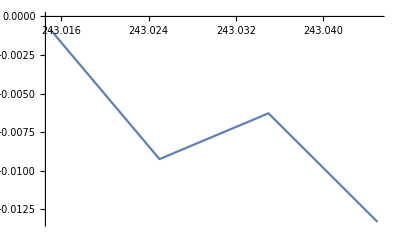

```mathematica
ListLinePlot@%
```

```mathematica
ParallelTable[{N[S,10],Block[{ω1,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]]},{S,58253.198,58253.199,0.001}]
```

0.859834

0.859834

0.859834

«1 more identical outputs»

{{58253.2,-1482.97},{58253.2,-2092.88}}

```mathematica
ParallelTable[{N[S,10],Block[{ω1,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]]},{S,58253.198,58253.199,0.001}]
```

0.859834

0.859834

0.859834

«1 more identical outputs»

{{58253.2,7.97792},{58253.2,7.97792}}

```mathematica
ParallelTable[{N[S,10],Block[{ω1,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]]},{S,58253.198,58253.199,0.001}]
```

0.859834

0.859834

0.859834

«1 more identical outputs»

{{58253.2,-745.468},{58253.2,-1050.42}}

```mathematica
ParallelTable[{N[S,10],Block[{ω1,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];
ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]]},{S,58253.198,58253.199,0.001}]
```

0.859834

0.859834

0.859834

«1 more identical outputs»

{{58253.2,-745.482},{58253.2,-1050.44}}

```mathematica
ParallelTable[Block[{ω1,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];If[(λ ω2)/(1-ω1+ω2)>0,NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,(ω2 λ)/(1-ω1+ω2)},{y,0,1}],0]+If[((1-λ) ω2)/(1-ω1+ω2)<1,NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,(ω2 (1-λ))/(1-ω1+ω2),1},{y,0,1}],0]-1/λ 2 NIntegrate[(ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[x/(ω2/(1-ω1+ω2))] ϕ1[x] ϕ2[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2)),{x,(If[#1>0,#1,0]&)[(ω2 λ)/(1-ω1+ω2)],(If[#1<1,#1,1]&)[(ω2 (1-λ))/(1-ω1+ω2)]}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,(If[#1>0,#1,0]&)[(ω2 λ)/(1-ω1+ω2)],(If[#1<1,#1,1]&)[(ω2 (1-λ))/(1-ω1+ω2)]},{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,(If[#1>0,#1,0]&)[(ω2 λ)/(1-ω1+ω2)],(If[#1<1,#1,1]&)[(ω2 (1-λ))/(1-ω1+ω2)]},{y,x/(ω2/(1-ω1+ω2))+λ,1}]],{S,58253.198,58253.199,0.001}]
```

0.859834

0.859834

0.859834

«1 more identical outputs»

{186.37,262.61}

```mathematica
ParallelTable[Block[{ω1,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];If[(λ ω2)/(1-ω1+ω2)>0,NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,(ω2 λ)/(1-ω1+ω2)},{y,0,1}],0]],{S,58253.198,58253.199,0.001}]
```

0.859834

0.859834

0.859834

«1 more identical outputs»

{4.40034×10^-27,4.39968×10^-27}

```mathematica
ParallelTable[Block[{ω1,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];If[((1-λ) ω2)/(1-ω1+ω2)<1,NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,(ω2 (1-λ))/(1-ω1+ω2),1},{y,0,1}],0]],{S,58253.198,58253.199,0.001}]
```

0.859834

0.859834

0.859834

«1 more identical outputs»

{2.34477×10^-8,2.34479×10^-8}

```mathematica
ParallelTable[Block[{ω1,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];-1/λ 2 NIntegrate[(ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[x/(ω2/(1-ω1+ω2))] ϕ1[x] ϕ2[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2)),{x,(If[#1>0,#1,0]&)[(ω2 λ)/(1-ω1+ω2)],(If[#1<1,#1,1]&)[(ω2 (1-λ))/(1-ω1+ω2)]}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,(If[#1>0,#1,0]&)[(ω2 λ)/(1-ω1+ω2)],(If[#1<1,#1,1]&)[(ω2 (1-λ))/(1-ω1+ω2)]},{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,(If[#1>0,#1,0]&)[(ω2 λ)/(1-ω1+ω2)],(If[#1<1,#1,1]&)[(ω2 (1-λ))/(1-ω1+ω2)]},{y,x/(ω2/(1-ω1+ω2))+λ,1}]],{S,58253.198,58253.199,0.001}]
```

0.859834

0.859834

0.859834

«1 more identical outputs»

{186.37,262.61}

#### Look here

```mathematica
ParallelTable[Block[{ω1,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];-1/λ 2 NIntegrate[(ϕ3[ω1-ω2+x (1-ω1+ω2)] ϕ4[(x (1-ω1+ω2))/ω2] ϕ1[x] ϕ2[(x+ω1-x ω1-ω2+x ω2)/ω1])/(ω2/(1-ω1+ω2)),{x,(ω2 λ)/(1-ω1+ω2),(ω2 (1-λ))/(1-ω1+ω2)}]+NIntegrate[(ω2 (1-ω1+ω2))/(x (-1+ω1-ω2)+y ω2)^2 ϕ3[ω1-ω2+x (1-ω1+ω2)] ϕ4[y] ϕ1[x] ϕ2[1+((-1+y) ω2)/ω1],{x,(ω2 λ)/(1-ω1+ω2),(ω2 (1-λ))/(1-ω1+ω2)},{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 (1-ω1+ω2))/(x (-1+ω1-ω2)+y ω2)^2 ϕ3[ω1-ω2+x (1-ω1+ω2)] ϕ4[y] ϕ1[x] ϕ2[1+((-1+y) ω2)/ω1],{x,(ω2 λ)/(1-ω1+ω2),(ω2 (1-λ))/(1-ω1+ω2)},{y,x/(ω2/(1-ω1+ω2))+λ,1}]],{S,58253.198,58253.199,0.001}]
```

0.887418

0.887418

0.859834

0.859834

{77.1333,77.1354}

```mathematica
ParallelTable[Table[Block[{ω1,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];-1/λ 2 NIntegrate[(ϕ3[ω1-ω2+x (1-ω1+ω2)] ϕ4[(x (1-ω1+ω2))/ω2] ϕ1[x] ϕ2[(x+ω1-x ω1-ω2+x ω2)/ω1])/(ω2/(1-ω1+ω2)),{x,(ω2 λ)/(1-ω1+ω2),(ω2 (1-λ))/(1-ω1+ω2)}]+NIntegrate[(ω2 (1-ω1+ω2))/(x (-1+ω1-ω2)+y ω2)^2 ϕ3[ω1-ω2+x (1-ω1+ω2)] ϕ4[y] ϕ1[x] ϕ2[1+((-1+y) ω2)/ω1],{x,(ω2 λ)/(1-ω1+ω2),(ω2 (1-λ))/(1-ω1+ω2)},{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 (1-ω1+ω2))/(x (-1+ω1-ω2)+y ω2)^2 ϕ3[ω1-ω2+x (1-ω1+ω2)] ϕ4[y] ϕ1[x] ϕ2[1+((-1+y) ω2)/ω1],{x,(ω2 λ)/(1-ω1+ω2),(ω2 (1-λ))/(1-ω1+ω2)},{y,x/(ω2/(1-ω1+ω2))+λ,1}]],{S,{243.015,243.025,243.035,243.045}^2}],{λ,Table[10^-m,{m,2,10,1}]}]
```

0.767344

0.767344

0.767344

«5 more identical outputs»

0.756591

0.756591

0.756591

«5 more identical outputs»

0.766863

0.756142

0.766863

0.756142

0.766863

0.756142

0.766863

0.756142

0.766863

0.756142

0.766863

0.756142

0.766863

0.756142

0.766863

0.756142

0.766383

0.755695

0.766383

0.755695

0.766383

0.755695

0.766383

0.755695

0.766383

0.755695

0.766383

0.755695

0.766383

0.755695

0.766383

0.755695

0.765904

0.755248

0.765904

0.755248

0.765904

0.755248

0.765904

0.755248

0.765904

0.755248

0.765904

0.755248

0.765904

0.755248

0.765904

0.755248

0.767344

0.756591

0.766863

0.756142

0.766383

0.755695

0.765904

0.755248

{{39.093,38.7541,38.4197,38.0897},{39.7053,39.3495,38.9988,38.6529},{39.7654,39.408,39.0556,38.7082},{39.7716,39.414,39.0615,38.7139},{39.7736,39.4162,39.0624,38.7162},{37.9604,37.6315,37.3055,36.9846},{1516.71,1494.02,1470.43,1445.96},{-106769.,-108521.,-110216.,-111854.},{-6.87103×10^7,-6.6796×10^7,-6.49435×10^7,-6.31507×10^7}}

```mathematica
ω2/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2)//Simplify
```

(ω2 (1-ω1+ω2))/(x (-1+ω1-ω2)+y ω2)^2

```mathematica
?ℳ1
```

```mathematica
ParallelTable[ℳ1[ω1,ω2p[ω1][M1,M2,M3,M4]][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4],{ω1,0.1,0.9,0.1}]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
{√S,EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {6.50982×10^-8,6.51048×10^-8}. NIntegrate obtained 2.18837×10^-15 and 2.95611×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99999999734797705763765491418130819335687714533023040530679281801,0.99999999734752591414205577349852835042105098084519454459950793535}. NIntegrate obtained 2177.04 and 800.959 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0125827,0.0125827}. NIntegrate obtained 0.000584738 and 0.000425501 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::zeroregion: Integration region {{1.,0.99999999999999999999999999997275243749960574466419003432897000423}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

{240.681,2.58769×10^6}

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]]
```

```mathematica
Block[{ω1,S,ω2,m=m1},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];If[ω1>1,ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,M2,M1,M3,M4]+ℳ0[1/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,M4,M3,M1,M2],ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]]+If[ω2>ω1,ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,M4,M3,M2,M1],ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,M2,M1,M4,M3]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,M3,M4,M1,M2]]]
```

2.47559

```mathematica
Block[{ω1,S,ω2,m=m1},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];If[ω1>1,ℐ1[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,M4,M3,M2,M1]+ℐ2[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,M4,M3,M1,M2],ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℐ2[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]]+If[ω2>ω1,ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]+ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],ℐ1[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1]+ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,M3,M4,M1,M2]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {6.50982×10^-8,6.51048×10^-8}. NIntegrate obtained 2.18837×10^-15 and 2.95611×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99999999734797705763765491418130819335687714533023040530679281801,0.99999999734752591414205577349852835042105098084519454459950793535}. NIntegrate obtained 2177.04 and 800.959 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0125827,0.0125827}. NIntegrate obtained 0.000584738 and 0.000425501 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

-462216.

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];Which[0<ω1<1&&ω2≥ω1,ℐ3[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ3[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma],ω2≥ω1&&ω1≥1,ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℐ3[(1+1/ω2-ω1/ω2) ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,Mb,Ma,Mc,Md],0<ω1<1&&ω1>ω2,ℐ3[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,Mb,Ma,Md,Mc],ω1≥1&&ω1>ω2,ℐ3[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb]+ℐ3[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999999999999999998369273566250875422125492455831169218}. NIntegrate obtained -515482. and 80671.1 for the integral and error estimates.

NIntegrate::zeroregion: Integration region {{1.,0.99999999999999999999999999997275243749960574466419003432897000423}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999810662305438375076468677767889263508772586860201548}. NIntegrate obtained -246994. and 8550.67 for the integral and error estimates.

3.04991×10^6

```mathematica
Block[{ω1,S,ω2,m=m1},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℐ2[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {6.50982×10^-8,6.51048×10^-8}. NIntegrate obtained 2.18837×10^-15 and 2.95611×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99999999734797705763765491418130819335687714533023040530679281801,0.99999999734752591414205577349852835042105098084519454459950793535}. NIntegrate obtained 2177.04 and 800.959 for the integral and error estimates.

-8591.27

```mathematica
Block[{ω1,S,ω2,m=m1},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];
ℐ1[1,1/ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]]
```

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]]
```

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ1[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1]]
```

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,M3,M4,M1,M2]]
```

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0125827,0.0125827}. NIntegrate obtained 0.000584738 and 0.000425501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {1.,0.99999996897772734775855906983249772081168149640006959089078009129}. NIntegrate obtained 26118.9 and 60519. for the integral and error estimates.

-104416.

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]]
```

```mathematica
Table[Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];-1/λ 2 NIntegrate[(ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[x/(ω2/(1-ω1+ω2))] ϕ1[x] ϕ2[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2)),{x,(If[#1>0,#1,0]&)[(ω2 λ)/(1-ω1+ω2)],(If[#1<1,#1,1]&)[(ω2 (1-λ))/(1-ω1+ω2)]}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,(If[#1>0,#1,0]&)[(ω2 λ)/(1-ω1+ω2)],(If[#1<1,#1,1]&)[(ω2 (1-λ))/(1-ω1+ω2)]},{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,(If[#1>0,#1,0]&)[(ω2 λ)/(1-ω1+ω2)],(If[#1<1,#1,1]&)[(ω2 (1-λ))/(1-ω1+ω2)]},{y,x/(ω2/(1-ω1+ω2))+λ,1}]],{λ,Table[10^-m,{m,2,10,1}]}]
```

{-3.17307,-5.44444,-7.6738,-9.89503,-12.1168,-14.3424,-16.7078,-21.661,-360.238}

```mathematica
Table[Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1 λ,ω1(1-λ)},{y,x/ω1+λ,1}]],{λ,Table[10^-m,{m,2,10,1}]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{675.995,11694.2,125038.,1.26118×10^6,1.26252×10^7,1.26268×10^8,1.2627×10^9,1.2627×10^10,1.2627×10^11}

```mathematica
Table[Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1 λ,ω1(1-λ)},{y,0,x/ω1-λ}]],{λ,Table[10^-m,{m,2,10,1}]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{980.802,12579.6,126511.,1.26324×10^6,1.26279×10^7,1.26272×10^8,1.2627×10^9,1.26271×10^10,1.26271×10^11}

```mathematica
Table[Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];-(2.NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1,{x,ω1 λ,ω1(1-λ)}])/λ],{λ,Table[10^-m,{m,2,10,1}]}]
```

{-2525.41,-25254.1,-252541.,-2.52541×10^6,-2.52541×10^7,-2.52541×10^8,-2.52541×10^9,-2.52541×10^10,-2.52541×10^11}

```mathematica
Table[Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4,x=0.5},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
-(2(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1)/λ+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{y,0,x/ω1-λ}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{y,x/ω1+λ,1}]],{λ,Table[10^-m,{m,2,10,1}]}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.50919955899142330010884770859701316578098449858874596785085486772}. NIntegrate obtained 3.27271×10^12 and 1.89191×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.50919956017177913077364537297411303280866498588430602012522285804}. NIntegrate obtained 3.27271×10^12 and 1.88191×10^7 for the integral and error estimates.

{-29312.9,-34678.9,-35224.4,-35278.9,-35284.4,-35280.9,-35594.3,-17672.5,-1.38074×10^6}

```mathematica
Table[Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4,opt},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
-(2.NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1,{x,ω1 λ,ω1(1-λ)},PrecisionGoal->10])/λ+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1 λ,ω1(1-λ)},{y,0,x/ω1-λ},PrecisionGoal->10]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1 λ,ω1(1-λ)},{y,x/ω1+λ,1},PrecisionGoal->10]],{λ,Table[10^-m,{m,2,10,1}]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 484382. and 0.0000513983 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 609802. and 0.0000757405 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 767697. and 0.000122023 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{-3.17307,-3.40416,-3.63415,-3.86311,-4.09112,-4.31827,-4.54467,-4.7704,-4.99555,-5.22021,-5.44444,-5.6683,-5.89186,-6.11516,-6.33824,-6.56114,-6.78388,-7.0065,-7.22901,-7.45143,-7.67379,-7.89608,-8.11832,-8.34052,-8.56268,-8.78482,-9.00694,-9.22903,-9.45112,-9.67319,-9.89524,-10.1173,-10.3393,-10.5614,-10.7834,-11.0054,-11.2275,-11.4495,-11.6715,-11.8935,-12.1156,-12.3376,-12.5596,-12.7816,-13.0036,-13.2255,-13.4474,-13.67,-13.8914,-14.1135,-14.3338,-14.5551,-14.7767,-15.0062,-15.2237,-15.4527,-15.6724,-15.8529,-16.1436,-16.2558,-16.7393,-16.8937,-16.7694,-17.6121,-17.1839,-17.7762,-20.4547,-15.7747,-21.8891,-17.9041,-8.39194,-39.1874,-68.6452,25.2971,-120.64,186.522,96.3192,-531.483,-228.938,500.926,-293.721}

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];-(2 NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1,{x,ω1 λ,ω1(1-λ)}])/λ+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1 λ,ω1(1-λ)},{y,0,x/ω1-λ}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1 λ,ω1(1-λ)},{y,x/ω1+λ,1}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,0,ω1 λ},{y,0,1}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1,1},{y,0,1}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1(1-λ),ω1},{y,0,x/ω1-λ}]-2/λ NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1,{x,ω1(1-λ),ω1}]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.98193329320104066793448733564777512100024285584677998829639111733,0.99999999999998595224991937118287426928140081609199350126410826833}. NIntegrate obtained 27.6356 and 0.00145172 for the integral and error estimates.

-1.92837×10^6

```mathematica
Table[Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];-(2 NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1,{x,ω1 λ,ω1(1-λ)}])/λ+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1 λ,ω1(1-λ)},{y,0,x/ω1-λ}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1 λ,ω1(1-λ)},{y,x/ω1+λ,1}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,0,ω1 λ},{y,0,1}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1,1},{y,0,1}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1(1-λ),ω1},{y,0,x/ω1-λ}]-2/λ NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1,{x,ω1(1-λ),ω1}]],{λ,Table[10^-m,{m,2,10,1}]}]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.1031×10^-25 and 2.02756×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.981933}. NIntegrate obtained 3.38177×10^-36 and 1.31325×10^-41 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.2789×10^-27 and 7.90439×10^-32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.981933}. NIntegrate obtained 2.04038×10^-38 and 5.56662×10^-43 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.20828×10^-29 and 7.75738×10^-34 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.981933}. NIntegrate obtained 1.92551×10^-40 and 1.74934×10^-45 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{623.585,{-868.613,-980.246,-991.512,-992.625,-989.382,-992.32,-9669.95,3911.96,-31558.7}}

```mathematica
Table[Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];-(2 NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1,{x,ω1 λ,ω1(1-λ)}])/λ+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1 λ,ω1(1-λ)},{y,0,x/ω1-λ}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1 λ,ω1(1-λ)},{y,x/ω1+λ,1}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,0,ω1 λ},{y,0,1}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1(1-λ),1},{y,0,1}](*+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1(1-λ),ω1},{y,0,x/ω1-λ}]-2/λ NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1,{x,ω1(1-λ),ω1}]*)],{λ,Table[10^-m,{m,2,10,1}]}]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.1031×10^-25 and 2.02756×10^-30 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.2789×10^-27 and 7.90439×10^-32 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.20828×10^-29 and 7.75738×10^-34 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{468.332,{-868.613,-980.246,-991.512,-992.625,-989.382,-992.32,-9669.95,3911.96,-31558.7}}

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,0,ω1 λ},{y,0,1}]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.2789×10^-27 and 7.90439×10^-32 for the integral and error estimates.

1.2789×10^-27

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1(1-λ),ω1},{y,0,x/ω1-λ}]]
```

0.981933

0.981933

0.96419

```mathematica
Table[Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1(1-λ),ω1},{y,0,x/ω1-λ}]-2/λ NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1,{x,ω1(1-λ),ω1}]],{λ,Table[10^-m,{m,2,10,1}]}]
```

{-1.03258,-0.975567,-0.965776,-0.964396,-0.964218,-0.964196,-0.964193,-0.964193,-0.964192}

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1(1-λ),1},{y,0,1}]]
```

0.981933

0.981933

1.4309×10^-12

```mathematica
Table[Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];-(2 NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1,{x,ω1 λ,ω1(1-λ)}])/λ+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1 λ,ω1(1-λ)},{y,0,x/ω1-λ}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1 λ,ω1(1-λ)},{y,x/ω1+λ,1}]],{λ,Table[10^-m,{m,2,10,1}]}]
```

{-3.17307,-5.44444,-7.6738,-9.89503,-12.1168,-14.3424,-16.7078,-21.661,-360.238}

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+1)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]]
```

0.833387

0.833387

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 1 recursive bisections in y near {x,y} = {0.844124,0.922062}. NIntegrate obtained 250.104 and 15.5334 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 1 recursive bisections in y near {x,y} = {0.844124,0.422062}. NIntegrate obtained 242.401 and 33.8283 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 1 recursive bisections in y near {x,y} = {7.03482×10^-8,0.422062}. NIntegrate obtained 1.20972×10^-27 and 6.86884×10^-28 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

1.85987×10^7

```mathematica
ϕ2[-0.0001]
```

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4,x=0.99,y},y=0.99;S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];Print@y;Print@ ϕ4[(x+ω2-ω1)/(1+ω2-ω1)];(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2]
```

```mathematica
ϕ2[1.0184001182742242]
```

```mathematica
λ=10^-5;
```

```mathematica
ParallelTable[{x,Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];-(2 (ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1)/λ+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{y,0,x/ω1-λ}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{y,x/ω1+λ,1}]]},{x,(Sin[π #]^9/2+0.5)&/@Range[0,1,0.01]}]
```

```mathematica
Drop[%75,-1]
```

```mathematica
NIntegrate[Interpolation[%80][x],{x,0,1}]
```

```mathematica
ListPlot[%80,Joined->True,PlotRange->All]
```

```mathematica
Block[{ω1,S,ω2,m=m1},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
Which[0<ω1<1&&ω2≥ω1,ℐ3[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,M4,M3,M2,M1]+ℐ3[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1],ω2≥ω1&&ω1≥1,ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℐ3[(1+1/ω2-ω1/ω2) ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,M2,M1,M3,M4],0<ω1<1&&ω1>ω2,ℐ3[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]+ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,M2,M1,M4,M3],ω1≥1&&ω1>ω2,ℐ3[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,M4,M3,M1,M2]+ℐ3[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,M3,M4,M1,M2]]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m1,M4,M3,M2,M1]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m1,M1,M2,M4,M3]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m1,M3,M4,M2,M1]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];ω2=ω2S[S][M1,M2,M3,M4];ℳ0[1/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m1,M4,M3,M1,M2]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m1,M3,M4,M1,M2]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][M2,M1,M3,M4]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][M2,M1,M4,M3]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][M1,M2,M4,M3]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][M3,M4,M1,M2]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];If[ω1^2+ω2+ω2^2<ω1+2 ω1 ω2,-4 g^2 (NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,x/(ω2/(1-ω1+ω2))+λ,1}]-(2 NIntegrate[(ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[x/(ω2/(1-ω1+ω2))] ϕ1[x] ϕ2[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2)),{x,0,1}])/λ),0]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];NIntegrate[(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2) ϕ3[ω1-ω2+x (1-ω1+ω2)] ϕ4[y] ϕ1[x] ϕ2[1+((-1+y) ω2)/ω1],{x,0,1},{y,0,1},MaxRecursion->50]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];NIntegrate[(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2) ϕ3[ω1-ω2+x (1-ω1+ω2)] ϕ4[y] ϕ1[x] ϕ2[1+((-1+y) ω2)/ω1],{x,0,1},{y,0,(x (1-ω1+ω2))/ω2-λ}]]
```

```mathematica
Block[{ω1,S,ω2,ex},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ex=(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2) ϕ1[ω1-ω2+x (1-ω1+ω2)] ϕ2[y] ϕ3[x] ϕ4[1+((-1+y) ω2)/ω1];NIntegrate[ex,{x,0,1},{y,(x (1-ω1+ω2))/ω2+λ,1},MaxRecursion->50,PrecisionGoal->15]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];(2 NIntegrate[(ϕ1[ω1-ω2+x (1-ω1+ω2)] ϕ2[(x (1-ω1+ω2))/ω2] ϕ3[x] ϕ4[(x+ω1-x ω1-ω2+x ω2)/ω1])/(ω2/(1-ω1+ω2)),{x,0,1}])/λ]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];Plot3D[ϕ1[ω1-ω2+x (1-ω1+ω2)] ϕ2[y] ϕ3[x] ϕ4[1+((-1+y) ω2)/ω1],{x,0,1},{y,0,1},PlotRange->All]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];Plot3D[(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2),{x,0,1},{y,0,1},PlotRange->All]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];Plot3D[(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2) ϕ1[ω1-ω2+x (1-ω1+ω2)] ϕ2[y] ϕ3[x] ϕ4[1+((-1+y) ω2)/ω1],{x,0,1},{y,0,1},PlotRange->All]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][M2,M1,M4,M3]]
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][M1,M2,M4,M3]]
```

```mathematica
Clear[M1,M2,M3,M4,ϕ1,ϕ2,ϕ3,ϕ4]
```

```mathematica
SetSharedVariable[M1,M2,M3,M4,ϕ1,ϕ2,ϕ3,ϕ4]
```

```mathematica
Table[{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[n1];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[n2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]],{n1,0,5,1},{n2,0,5,1}]
```

```mathematica
ParallelTable[ℳ1[M1,M2,M3,M4][ω1/(ω2p[ω1][M1,M2,M3,M4]),1/(ω2p[ω1][M1,M2,M3,M4])][ϕ1,ϕ2,ϕ3,ϕ4],{ω1,0.1,0.9,0.1}]
```

```mathematica
?EXPR
```

```mathematica
FindRoot[√(Sω1[ω1][M1,M2,M3,M4])==241.137,{ω1,0.9,0.99}]
```

```mathematica
Reduce[1/(ω2p[ω1][M1,M2,M3,M4])>(1-ω1+ω2p[ω1][M1,M2,M3,M4])/(ω2p[ω1][M1,M2,M3,M4])&&(1-ω1+ω2p[ω1][M1,M2,M3,M4])/(ω2p[ω1][M1,M2,M3,M4])>1,ω1]
```

```mathematica
Block[{ω1,ω2},ω2=ω2n[ω1][M1,M2,M3,M4]; ω1/.FindInstance[1/ω2>(1-ω1+ω2)/ω2&&(1-ω1+ω2)/ω2>1&&0<ω1<1,ω1,100]]
```

```mathematica
Block[{ω1,ω2},ω2=ω2n[ω1][M1,M2,M3,M4]; ω1/.FindInstance[ω2>ω1&&ω1>1&&0<ω1<1,ω1,100]]
```

```mathematica
Block[{ω1,ω2},ω2=ω2n[ω1][M1,M2,M3,M4]; ω1/.FindInstance[(1-ω1+ω2)/ω1>1/ω1&&1/ω1>1&&0<ω1<1,ω1,100]]
```

```mathematica
ω1/.FindInstance[ω2p[ω1][M1,M2,M3,M4]>ω1&&ω1>1&&0<ω1<1,ω1,100]
```

```mathematica
Block[{ω1=0.1,ω2},ω2=ω2n[ω1][M1,M2,M3,M4]; Print[1/ω2>(1-ω1+ω2n[ω1][M1,M2,M3,M4])/(ω2n[ω1][M1,M2,M3,M4])&&(1-ω1+ω2n[ω1][M1,M2,M3,M4])/(ω2n[ω1][M1,M2,M3,M4])>1&&0<ω1<1];NIntegrate[(M3^2+M4^2/(ω1/(1-ω1+ω2))+M1^2/(x-ω2/(1-ω1+ω2))+M1^2/(x-1)-M1^2/(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))-M1^2/x) ϕ1[(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[x/(ω2/(1-ω1+ω2))] ϕ3[x] ϕ4[(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))],{x,0,1}]]
```

```mathematica
Plot[ω2n[ω1][M1,M2,M3,M4],{ω1,0,1}]
```

```mathematica
Plot[√(Sω1[ω1][M1,M2,M3,M4]),{ω1,0,1}]
```

```mathematica
Block[{ω1=0.8829424796893336,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];ℳone[ω1,ω2][M1][ϕ1,ϕ2,ϕ3,ϕ4]]
```

```mathematica
Block[{ω1=0.907479105147823,ω2,Sen},ω2=ω2p[ω1][M1,M2,M3,M4];Sen=√(Sω1[ω1][M1,M2,M3,M4]);If[ω2∈Reals&&Sen∈Reals,Print["ω1=",ω1,"    ω2=",ω2];{Sen,ℳone[ω1,ω2][M1][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: ω1=",ω1]]]
```

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];𝒞[ℳ0[ω1,ω2]][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]]
```

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];ℳ1[M1][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]]
```

```mathematica
Plot[(ω2p[ω1][M1,M2,M3,M4])/ω1,{ω1,1,1.3}]
```

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,1}]]
```

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,x/ω1-λ}]+NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,x/ω1+λ,1}]-2/λ NIntegrate[1/ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[((x/ω1-1) ω1+ω2)/ω2],{x,0,1}]]
```

```mathematica
NI1[ω1_,ω2_][x_?NumberQ]:=NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{y,0,(ω1-ω2+x ω2)/ω1-λ}]
NI2[ω1_,ω2_][x_?NumberQ]:=NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{y,(ω1-ω2+x ω2)/ω1+λ,1}]
```

```mathematica
λ=10^-4;
```

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(NIntegrate[NI1[ω1,ω2][x],{x,0,1}]+NIntegrate[NI2[ω1,ω2][x],{x,0,1}]-2/λ NIntegrate[ω1 ω2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,0,1}])]
```

```mathematica
Table[Block[{ω1=0.3,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(NIntegrate[1/(y-x)^2 ϕ1[x ω2]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,λ,1-λ},{y,0,x-λ}]+NIntegrate[1/(y-x)^2 ϕ1[x ω2]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,λ,1-λ},{y,x+λ,1}]-2/λ NIntegrate[ ϕ1[x ω2]ϕ2[x]ϕ3[x ω1]ϕ4[x],{x,λ,1-λ}])],{λ,Table[10^-m,{m,2,7,1}]}]
```